# Supplemental

## Estimated Judge Reliabilities for Weighted Bradley-Terry-Luce Are Not Reliable

This notebook offers explorative examples of the behavior analyzed in the paper “Estimated Judge Reliabilities for Weighted Bradley-Terry-Luce Are Not Reliable.” While the full data is processed in the accompanying Julia files, this notebook serves as a dissimilar implementation, verifying the core elements and mathematics.

## Foundations

Before running the examples, we define the basic components we will use throughout the notebook. This mostly corresponds with Section 2 in the paper.

### Bradley-Terry-Luce (BTL)

We define the single pair probability (Eq. 1), denoted as Pr_BTL, and then, for convenience, take the negative log-likelihood of that single expression, denoted as L_BTL (Eq. 2). In the equations, we use ςk and ςj to refer to the estimated values of stimuli s_k and s_j on the latent scale respectively, while Δς to refers to a difference.

```mathematica
Subscript[Pr, BTL][Δς_]:=1/(1+Exp[-Δς])
Subscript[Pr, BTL][ςk_,ςj_]:=Subscript[Pr, BTL][ςk-ςj]
Subscript[L, BTL][Δς_]:=-Log[Subscript[Pr, BTL][Δς]]
Subscript[L, BTL][ςk_,ςj_]:=Subscript[L, BTL][ςk-ςj]
```

We can see the sigmoid shape by plotting Pr_BTL:

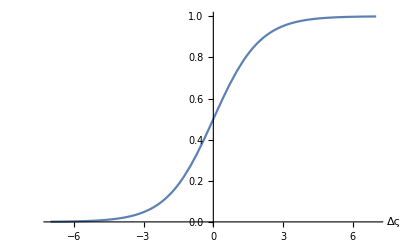

```mathematica
Plot[Subscript[Pr, BTL][Δς], {Δς, -7, 7}, AxesLabel->Automatic]
```

### Chen et al.’s Crowd-BT

These equations calculate the single pair probability (Eq. 4) and negative log-likelihood for Chen et al.’s Crowd-BT.

```mathematica
Subscript[Pr, CrowdBT][Δς_, η_] := η*Subscript[Pr, BTL][Δς] + (1-η)*(1-Subscript[Pr, BTL][Δς])
Subscript[Pr, CrowdBT][ςk_,ςj_, η_] := Subscript[Pr, CrowdBT][ςk - ςj, η]
Subscript[L, CrowdBT][Δς_, η_] := -Log[Subscript[Pr, CrowdBT][Δς, η]]
Subscript[L, CrowdBT][ςk_,ςj_, η_] := Subscript[L, CrowdBT][ςk - ςj, η]
```

We can visualize the effect of varying η (Fig. 1):

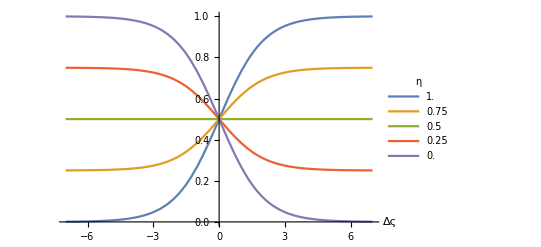

```mathematica
Plot[Evaluate@Table[Subscript[Pr, CrowdBT][Δς, η],{η, 1, 0, -0.25}],{Δς,-7, 7}, AxesLabel->Automatic,PlotLegends->LineLegend[Table[η,{η, 1, 0, -0.25}],LegendLabel->η]]
```

The differences can also be appreciated in 3D, especially when the delta is large:

```mathematica
Plot3D[Subscript[Pr, CrowdBT][Δς, η], {Δς, -20, 20}, {η, 0, 1}, AxesLabel->Automatic]
```

-Graphics3D-

### O’Donovan et al.

Finally, we implement the components for O’Doonovan et al.’s method (Eq. 5)

```mathematica
Subscript[Pr, ODonovan][Δς_, μ_] := 1 / (1 + Exp[-μ * Δς])
Subscript[Pr, ODonovan][ςk_,ςj_, μ_] := Subscript[Pr, ODonovan][ςk - ςj, μ]
Subscript[L, ODonovan][Δς_, μ_] := -Log[Subscript[Pr, ODonovan][Δς, μ]]
Subscript[L, ODonovan][ςk_,ςj_, μ_] := Subscript[L, ODonovan][ςk - ςj, μ]
```

As with Crowd-BT, we can visualize changes in μ (Fig. 1):

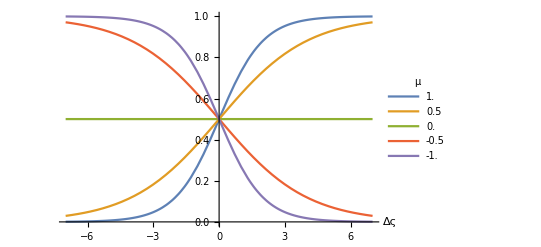

```mathematica
Plot[Evaluate@Table[Subscript[Pr, ODonovan][Δς, μ],{μ, 1, -1, -0.5}],{Δς,-7, 7}, AxesLabel->Automatic, PlotLegends->LineLegend[Table[μ,{μ, 1, -1, -0.5}],LegendLabel->μ]]
```

```mathematica
Plot3D[Subscript[Pr, ODonovan][Δς, μ], {Δς, -20, 20}, {μ, -1, 1}, AxesLabel->Automatic]
```

-Graphics3D-

### Mease’s Penalty

With the single pair components defined for the 3 study methods, we can turn to Mease’s penalty (Eq. 3). Although formulated as adding a dummy item, s_0, that is given one win and one loss against every other item, because ς_0=0, can simply set the equations to be relative to 0.  For a single term, this gives us the following equations:

```mathematica
Subscript[L, 0][ςk_] := Subscript[L, BTL][ςk,0] + Subscript[L, BTL][0,ςk]
Subscript[L, 0][ςk_, λ_] := λ * Subscript[L, 0][ςk]
```

It is often instructive to have a very small penalty which helps to uniquely identify the solutions. Here, we use 1E-6:

```mathematica
Subscript[λ, Default]:= 1*^-6
```

A quick remark about Mease’s Penalty and λ

Mathematically, Mease’s penalty  is similar to |ς|, and thus may be many times larger than loss due to changes in probability, such as in the examples above.

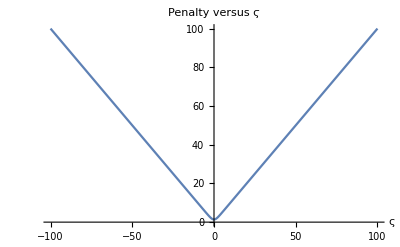

```mathematica
Plot[Subscript[L, 0][ς], {ς, -100, 100}, PlotLabel->"Penalty versus ϛ",AxesLabel->Automatic]
```

Depending on the relative number of decisions, this regularization can be very strong . We can generalize the penalty by introducing a scaling factor λ, where the original version corresponds to λ = 1.

A small value for λ can be appropriate because the point of λ is simply to uniquely identify the solution and avoid discontinuous items.  The problem with Mease’s formulation is that with a large value of λ, decisions with equivalent sampled probabilities are not proportional in the final solution.

Consider an example with 4 stimuli {s_1, s_2, s_3, s_4}, and two pairs {(s_1, s_2), (s_1, s_3),(s_3, s_4)} where (s_1, s_2) and (s_3, s_4) share the same 2/3 votes (66%) and (s_1, s_3) retains its unanimity (100%). We expect (s_1, s_2) and (s_3, s_4) to have approximately the same distance on the latent scale because they have the vote fraction.  This follows from Thrustone’s Law of Comparable Judgements.

```mathematica
Subscript[Subscript[L, BTL], Mease][ς1_,ς2_,ς3_, ς4_, λ_] :=3*Subscript[L, BTL][ς3,ς1] + Subscript[L, BTL][ς1,ς2] + 2*Subscript[L, BTL][ς2,ς1] + Subscript[L, BTL][ς3,ς4] + 2*Subscript[L, BTL][ς4,ς3]+ λ*(Subscript[L, 0][ς1] + Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+Subscript[L, 0][ς4])
```

For convenience, we will the final likelihood in minMease0 and the scale values in solMease0, where the 0 references λ = 0. We solve for the minimum using the same limits as in the paper [-100, 100].

```mathematica
{minMease0, solMease0} = FindMinimum[{Subscript[Subscript[L, BTL], Mease][ς1, ς2, ς3, ς4, 0], -100≤ς1≤100, -100≤ς2≤100, -100≤ς3≤100, -100≤ς4≤100}, {ς1, ς2,ς3, ς4}]
```

{3.81909,{ς1→-8.17639,ς2→-7.48324,ς3→7.48324,ς4→8.17639}}

The differences in the latent scale are:

```mathematica
{ N[ς2-ς1],N[ς4-ς3]}  /. solMease0
```

{0.693147,0.693147}

Which yields the following probabilities:

```mathematica
{Subscript[Pr, BTL][ς2, ς1], Subscript[Pr, BTL][ς3,ς1],Subscript[Pr, BTL][ς4 , ς3]}  /. solMease0
```

{0.666667,1.,0.666667}

These are the results we expect: the order is [s_1, s_2, s_3, s_4], (s_1, s_2) and (s_3, s_4) have approximately the same distance on the latent scale, and thus, the recovered probabilities match the input values.

This changes when we use a larger value for λ.  Let’s repeat the process, but setting λ = 1.

```mathematica
{minMease1, solMease1} = FindMinimum[{Subscript[Subscript[L, BTL], Mease][ς1, ς2, ς3, ς4, 1], -100≤ς1≤100, -100≤ς2≤100, -100≤ς3≤100, -100≤ς4≤100}, {ς1, ς2,ς3, ς4}]
```

{10.4881,{ς1→-1.01392,ς2→-0.181585,ς3→0.46204,ς4→0.688172}}

The differences in the latent scale are now:

```mathematica
{N[ς2 -ς1], N[ς4 -ς3]}/. solMease1
```

{0.832333,0.226132}

Even though we expected the relative distance between the pairs (s_1, s_2) and (s_3, s_4) to be approximately the same, they no longer are: the difference in (s_1, s_2) is almost 4 times as large as the difference in (s_3, s_4).  All we changed about the problem was whether or not we enforced the penalty.

This yields the following probabilities:

```mathematica
{ Subscript[Pr, BTL][ς2 , ς1],Subscript[Pr, BTL][ς3,ς1],Subscript[Pr, BTL][ς4 , ς3 ]}/. solMease1
```

{0.696848,0.813961,0.556293}

We will show more detailed computation later, but this should provide some insight into what happens with Table 1 in Section 4.3.

## Section 3: Core Behavior

With the foundations complete, we show the core behavior with two parties, (u_1, u_2), and a single decision between two stimuli, (s_1, s_2) .  To make these numerically tractable, we restrict the values to lie in ϛ ∈ [-10, 10].

#### Agreement

Starting with the BTL, we have:

```mathematica
Subscript[Subscript[L, BTL], Agree][ς1_,ς2_, λ_] := 2* Subscript[L, BTL][ς2,ς1] + λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2])
```

We solve for the minimum and the scale values for λ = {0, 1}.  We set the precision goal to be larger than the default because otherwise the solver will exit before reaching the limit, even though doing  so is optimal.  Note that with λ = 1, as expected, the penalty prevents the ϛ values from reaching the limits.

```mathematica
{minBTLAgree0, solBTLAgree0}  = FindMinimum[{Subscript[Subscript[L, BTL], Agree][ς1,ς2, 0], -10≤ς1≤10,-10≤ς2≤10}, {ς1, ς2}, PrecisionGoal->20]
{minBTLAgree1, solBTLAgree1}  = FindMinimum[{Subscript[Subscript[L, BTL], Agree][ς1,ς2, 1], -10≤ς1≤10,-10≤ς2≤10}, {ς1, ς2}, PrecisionGoal->20]
```

FindMinimum::acceptlev: Solved to acceptable level.

{4.12231×10^-9,{ς1→-10.,ς2→10.}}

{3.45027,{ς1→-0.756308,ς2→0.756308}}

For Chen et al.’s Crowd-BT we have:

```mathematica
Subscript[Subscript[L, CrowdBT], Agree][ς1_,ς2_, η1_,η2_, λ_] :=  Subscript[L, CrowdBT][ς2,ς1,η1 ] + Subscript[L, CrowdBT][ς2,ς1,η2 ]+λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2])
```

We define an η_Initialbecause Crowd-BT is often sensitive to this value.  Here, it is not all that important, but it plays a more significant role later in the notebook.  A value slightly smaller than 1 is typically helpful.

```mathematica
Subscript[η, Initial]= 0.9;
```

Solving yields:

```mathematica
{minCrowdBTAgree0, solCrowdBTAgree0}  = FindMinimum[{Subscript[Subscript[L, CrowdBT], Agree][ς1,ς2,η1,η2, 0], -10≤ς1≤10,-10≤ς2≤10,0≤η1≤1, 0≤η2≤1}, {ς1, ς2,{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]}}, PrecisionGoal->20]
{minCrowdBTAgree1, solCrowdBTAgree1}  = FindMinimum[{Subscript[Subscript[L, CrowdBT], Agree][ς1,ς2,η1,η2, 1], -10≤ς1≤10,-10≤ς2≤10,0≤η1≤1, 0≤η2≤1}, {ς1, ς2,{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]}}, PrecisionGoal->20]
```

FindMinimum::acceptlev: Solved to acceptable level.

{4.12231×10^-9,{ς1→-10.,ς2→10.,η1→1.,η2→1.}}

FindMinimum::sdir: Search direction has become too small.

{3.45027,{ς1→-0.756308,ς2→0.756308,η1→1.,η2→1.}}

This is, as expected, the same result as the BTL solution.

O’Donovan et al’s solution is similar to Crowd-BT

```mathematica
Subscript[Subscript[L, ODonovan], Agree][ς1_,ς2_, μ1_,μ2_, λ_] :=  Subscript[L, ODonovan][ς2,ς1,μ1 ] + Subscript[L, ODonovan][ς2,ς1,μ2]+λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2])
```

Unlike Crowd-BT, O’Donovan et al’s solution is not as sensitive to the initial value of μ.  We typically set it to 1, since this would be equivalent to the BTL.

```mathematica
Subscript[μ, Initial] = 1;
```

We restrict the value of μ to [-2, 2] because, as before, the solver will reach an acceptable value well before hitting the theoretical minimum.

```mathematica
{minODonovanAgree0, solODonovanAgree0}  = FindMinimum[{Subscript[Subscript[L, ODonovan], Agree][ς1,ς2,μ1,μ2, 0], -10≤ς1≤10,-10≤ς2≤10,-2≤μ1≤2, -2≤μ2≤2}, {ς1, ς2,{μ1,Subscript[μ, Initial]},{μ2,Subscript[μ, Initial]}}, PrecisionGoal->20]
{minODonovanAgree1, solODonovanAgree1}  = FindMinimum[{Subscript[Subscript[L, ODonovan], Agree][ς1,ς2,μ1,μ2, 1], -10≤ς1≤10,-10≤ς2≤10,-2≤μ1≤2, -2≤μ2≤2}, {ς1, ς2,{μ1,Subscript[μ, Initial]},{μ2,Subscript[μ, Initial]}}, PrecisionGoal->20]
```

FindMinimum::acceptlev: Solved to acceptable level.

{1.66089×10^-13,{ς1→-8.36525,ς2→8.33536,μ1→1.80347,μ2→1.80347}}

{3.12258,{ς1→-0.625459,ς2→0.625459,μ1→2.,μ2→2.}}

To show this is the case, we can plug in the known theoretical solution and compare it to the numerically computed one.

```mathematica
N[Subscript[Subscript[L, ODonovan], Agree][-10, 10, 2, 2, 0]]<N[Subscript[Subscript[L, ODonovan], Agree][ς1,ς2,μ1,μ2, 0]]/.solODonovanAgree0
```

True

#### Disagreement

The disagreement works similarly to the agreement values above, but we will start the solution with ς1=-0.1 and ς2=0.1 so that the results are predictable.

```mathematica
Subscript[Subscript[L, BTL], Disagree][ς1_,ς2_, λ_] := Subscript[L, BTL][ς2,ς1] + Subscript[L, BTL][ς1,ς2]+ λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2])
```

```mathematica
{minBTLDisagree0, solBTLDisagree0}  = FindMinimum[{Subscript[Subscript[L, BTL], Disagree][ς1,ς2, 0], -10≤ς1≤10,-10≤ς2≤10}, {{ς1,-0.1},{ς2,0.1}}, PrecisionGoal->20]
{minBTLDisagree1, solBTLDisagree1}  = FindMinimum[{Subscript[Subscript[L, BTL], Disagree][ς1,ς2, 1], -10≤ς1≤10,-10≤ς2≤10}, {{ς1,-0.1},{ς2,0.1}}, PrecisionGoal->20]
```

{1.38629,{ς1→1.02399×10^-16,ς2→8.63928×10^-17}}

{4.15888,{ς1→-4.83566×10^-18,ς2→-3.34191×10^-17}}

As expected, the BTL solution converges to both stimuli having the same value.

```mathematica
Subscript[Subscript[L, CrowdBT], Disagree][ς1_,ς2_, η1_,η2_, λ_] :=  Subscript[L, CrowdBT][ς2,ς1,η1 ] + Subscript[L, CrowdBT][ς1,ς2,η2 ]+λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2])
```

```mathematica
{minCrowdBTDisagree0, solCrowdBTDisagree0}  = FindMinimum[{Subscript[Subscript[L, CrowdBT], Disagree][ς1,ς2,η1,η2,0], -10≤ς1≤10,-10≤ς2≤10,0≤η1≤1, 0≤η2≤1}, {{ς1, -0.1}, {ς2, 0.1},{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]}}]
```

{1.17956×10^-6,{ς1→-7.24554,ς2→7.24554,η1→1.,η2→8.09091×10^-8}}

As noted in the paper, the symmetry means that our starting conditions controls which judge is reliable and which is not.  Here, we flip the sign of the starting values for ϛ, which results in the judges switching reliability estimates.

```mathematica
FindMinimum[{Subscript[Subscript[L, CrowdBT], Disagree][ς1,ς2,η1,η2,0], -10≤ς1≤10,-10≤ς2≤10,0≤η1≤1, 0≤η2≤1}, {{ς1, 0.1}, {ς2, -0.1},{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]}}]
```

{1.17956×10^-6,{ς1→7.24554,ς2→-7.24554,η1→8.09091×10^-8,η2→1.}}

The case is similar for O’Donovan et al.’s method

```mathematica
Subscript[Subscript[L, ODonovan], Disagree][ς1_,ς2_, μ1_,μ2_, λ_] :=  Subscript[L, ODonovan][ς2,ς1,μ1 ] + Subscript[L, ODonovan][ς1,ς2,μ2]+λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2])
```

```mathematica
{minODonovanDisagree0, solODonovanDisagree0}  = FindMinimum[{Subscript[Subscript[L, ODonovan], Disagree][ς1,ς2,μ1,μ2, 0], -10≤ς1≤10,-10≤ς2≤10,-2≤μ1≤2, -2≤μ2≤2}, {{ς1,-0.1}, {ς2,0.1},{μ1,Subscript[μ, Initial]},{μ2,Subscript[μ, Initial]}}, PrecisionGoal->20]
{minODonovanDisagree1, solODonovanDisagree1}  = FindMinimum[{Subscript[Subscript[L, ODonovan], Disagree][ς1,ς2,μ1,μ2, 1], -10≤ς1≤10,-10≤ς2≤10,-2≤μ1≤2, -2≤μ2≤2}, {{ς1,-0.1}, {ς2,0.1},{μ1,Subscript[μ, Initial]},{μ2,Subscript[μ, Initial]}}, PrecisionGoal->20]
```

FindMinimum::acceptlev: Solved to acceptable level.

{1.77858×10^-13,{ς1→-8.27206,ς2→8.33826,μ1→1.80953,μ2→-1.80878}}

{3.12258,{ς1→-0.625459,ς2→0.625459,μ1→2.,μ2→-2.}}

## Section 4: Creating Dictators

This example corresponds to Section 4 in the paper, where  we have n judges and n+1 stimuli.  All of the judges have a single “error”  that corresponds to their index.  Conceptually each judge should be equally reliable since they make an equally bad error.  Unfortunately, this will not be the result.

We identify the equations using the label "[method]_(Dictators, [n])” where [method] will be {BTL, CrowdBT, ODonovan} corresponding to the model being used and [n] is the number of judges.

### Bradley-Terry-Luce

With four different judges, for every pair, we always have three judges who agree and one that disagrees.

We can create the patterns for 4 and 5 judges, since this will be the region of interest for the other methods. Note that we can simply scale the (n-1) decisions where the judges agree to simplify the equations.

```mathematica
Subscript[Subscript[L, BTL], Dictators,4][ς1_,ς2_,ς3_, ς4_, ς5_, λ_] :=3*( Subscript[L, BTL][ς2,ς1]+ Subscript[L, BTL][ς3,ς2] +Subscript[L, BTL][ς4,ς3]+Subscript[L, BTL][ς5,ς4]) +Subscript[L, BTL][ς1,ς2]+Subscript[L, BTL][ς2,ς3]+ + Subscript[L, BTL][ς3,ς4]+Subscript[L, BTL][ς4,ς5] + λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5])
Subscript[Subscript[L, BTL], Dictators,5][ς1_,ς2_,ς3_, ς4_, ς5_,ς6_,  λ_] :=4*(Subscript[L, BTL][ς2,ς1]+ Subscript[L, BTL][ς3,ς2] +Subscript[L, BTL][ς4,ς3]+Subscript[L, BTL][ς5,ς4]+Subscript[L, BTL][ς6,ς5]) +Subscript[L, BTL][ς1,ς2]+Subscript[L, BTL][ς2,ς3]+ + Subscript[L, BTL][ς3,ς4]+Subscript[L, BTL][ς4,ς5]+ Subscript[L, BTL][ς5,ς6] + λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6])
```

Now we can solve for the minimum and the scale values

```mathematica
Subscript[λ, Subscript[BLT, Dictators]]= Subscript[λ, Default];
```

```mathematica
{minBTLDictators4, solBTLDictators4}  = FindMinimum[{Subscript[Subscript[L, BTL], Dictators,4][ς1,ς2,ς3, ς4,ς5, Subscript[λ, Subscript[BLT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100}, {ς1, ς2, ς3,ς4,ς5}]
```

{8.99737,{ς1→-2.19718,ς2→-1.09857,ς3→0.000043317,ς4→1.09865,ς5→2.19727}}

```mathematica
{minBTLDictators5, solBTLDictators5}  = FindMinimum[{Subscript[Subscript[L, BTL], Dictators,5][ς1,ς2,ς3, ς4,ς5, ς6, Subscript[λ, Subscript[BLT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100}, {ς1, ς2, ς3,ς4,ς5,ς6}]
```

{12.5101,{ς1→-3.46563,ς2→-2.07934,ς3→-0.693044,ς4→0.693247,ς5→2.07954,ς6→3.46583}}

We can see that the optimal latent scale is symmetric about 0 using the virtual node formulation, and we can see that the distances between the values are approximately uniform.  We say approximately because with the λ penalty, the scale gets compressed a bit toward 0; when λ=0, the resulting absolute values may vary, but the distances between the stimuli will be uniform.  Try changing λ_BTL_Dictators to see this effect.

The following expressions compute the distance between neighboring scale values:

```mathematica
{N[ς2 -ς1], N[ς4 -ς3 ],N[ς5 -ς4 ]}/. solBTLDictators4
```

{1.09861,1.09861,1.09861}

```mathematica
{N[ς2 -ς1 ], N[ς4 -ς3],N[ς5 -ς4],N[ς6 -ς5]}/. solBTLDictators5
```

{1.38629,1.38629,1.38629,1.38629}

### Chen el al.’s Crowd-BT

We now compute the results from Section 4.1.  Unlike in the BTL case above, we enumerate all of the votes because of the judge reliabilities. Because Crowd-BT will no exhibit the equality behavior, we show the results for n={4,5,6}.  We have additional cases in julia/input/dictators/symmetric to demonstrate the results with n={10, 25}.

```mathematica
Subscript[Subscript[L, CrowdBT], Dictators,4][ς1_,ς2_,ς3_, ς4_, ς5_, η1_,η2_,η3_, η4_,λ_] := Subscript[L, CrowdBT][ς1,ς2, η1] + Subscript[L, CrowdBT][ς3,ς2, η1] +Subscript[L, CrowdBT][ς4,ς3, η1] + Subscript[L, CrowdBT][ς5,ς4, η1]+Subscript[L, CrowdBT][ς2,ς1, η2] + Subscript[L, CrowdBT][ς2,ς3, η2] +Subscript[L, CrowdBT][ς4,ς3, η2] + Subscript[L, CrowdBT][ς5,ς4, η2]+Subscript[L, CrowdBT][ς2,ς1, η3] + Subscript[L, CrowdBT][ς3,ς2, η3] +Subscript[L, CrowdBT][ς3,ς4, η3] + Subscript[L, CrowdBT][ς5,ς4, η3]+Subscript[L, CrowdBT][ς2,ς1, η4] + Subscript[L, CrowdBT][ς3,ς2, η4] +Subscript[L, CrowdBT][ς4,ς3,η4] + Subscript[L, CrowdBT][ς4,ς5, η4]+ λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5])
Subscript[Subscript[L, CrowdBT], Dictators,5][ς1_,ς2_,ς3_, ς4_, ς5_, ς6_,η1_,η2_,η3_, η4_,η5_,λ_] := Subscript[L, CrowdBT][ς1,ς2, η1] + Subscript[L, CrowdBT][ς3,ς2, η1] +Subscript[L, CrowdBT][ς4,ς3, η1] + Subscript[L, CrowdBT][ς5,ς4, η1] +Subscript[L, CrowdBT][ς6,ς5, η1] +Subscript[L, CrowdBT][ς2,ς1, η2] + Subscript[L, CrowdBT][ς2,ς3, η2] +Subscript[L, CrowdBT][ς4,ς3, η2] + Subscript[L, CrowdBT][ς5,ς4, η2]+Subscript[L, CrowdBT][ς6,ς5, η2] +Subscript[L, CrowdBT][ς2,ς1, η3] + Subscript[L, CrowdBT][ς3,ς2, η3] +Subscript[L, CrowdBT][ς3,ς4, η3] + Subscript[L, CrowdBT][ς5,ς4, η3]+Subscript[L, CrowdBT][ς6,ς5, η3] +Subscript[L, CrowdBT][ς2,ς1, η4] + Subscript[L, CrowdBT][ς3,ς2, η4] +Subscript[L, CrowdBT][ς4,ς3,η4] + Subscript[L, CrowdBT][ς4,ς5, η4]+Subscript[L, CrowdBT][ς6,ς5, η4] + Subscript[L, CrowdBT][ς2,ς1, η5] + Subscript[L, CrowdBT][ς3,ς2, η5] +Subscript[L, CrowdBT][ς4,ς3,η5] + Subscript[L, CrowdBT][ς5,ς4, η5]+Subscript[L, CrowdBT][ς6,ς5, η5]+  λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6])
Subscript[Subscript[L, CrowdBT], Dictators,6][ς1_,ς2_,ς3_, ς4_, ς5_, ς6_,ς7_,η1_,η2_,η3_, η4_,η5_,η6_,λ_] := Subscript[L, CrowdBT][ς1,ς2, η1] + Subscript[L, CrowdBT][ς3,ς2, η1] +Subscript[L, CrowdBT][ς4,ς3, η1] + Subscript[L, CrowdBT][ς5,ς4, η1] +Subscript[L, CrowdBT][ς6,ς5, η1] +Subscript[L, CrowdBT][ς7,ς6, η1]+Subscript[L, CrowdBT][ς2,ς1, η2] + Subscript[L, CrowdBT][ς2,ς3, η2] +Subscript[L, CrowdBT][ς4,ς3, η2] + Subscript[L, CrowdBT][ς5,ς4, η2]+Subscript[L, CrowdBT][ς6,ς5, η2] +Subscript[L, CrowdBT][ς7,ς6, η2]+Subscript[L, CrowdBT][ς2,ς1, η3] + Subscript[L, CrowdBT][ς3,ς2, η3] +Subscript[L, CrowdBT][ς3,ς4, η3] + Subscript[L, CrowdBT][ς5,ς4, η3]+Subscript[L, CrowdBT][ς6,ς5, η3] +Subscript[L, CrowdBT][ς7,ς6, η3]+Subscript[L, CrowdBT][ς2,ς1, η4] + Subscript[L, CrowdBT][ς3,ς2, η4] +Subscript[L, CrowdBT][ς4,ς3,η4] + Subscript[L, CrowdBT][ς4,ς5, η4]+Subscript[L, CrowdBT][ς6,ς5, η4] +Subscript[L, CrowdBT][ς7,ς6, η4]+ Subscript[L, CrowdBT][ς2,ς1, η5] + Subscript[L, CrowdBT][ς3,ς2, η5] +Subscript[L, CrowdBT][ς4,ς3,η5] + Subscript[L, CrowdBT][ς5,ς4, η5]+Subscript[L, CrowdBT][ς6,ς5, η5]+ Subscript[L, CrowdBT][ς7,ς6, η5]+ Subscript[L, CrowdBT][ς2,ς1, η6] + Subscript[L, CrowdBT][ς3,ς2, η6] +Subscript[L, CrowdBT][ς4,ς3,η6] + Subscript[L, CrowdBT][ς5,ς4, η6]+Subscript[L, CrowdBT][ς5,ς6, η6]+ Subscript[L, CrowdBT][ς6,ς7, η6]+ λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6]+ Subscript[L, 0][ς7])
```

As before, we set a value of λ to uniquely identify the solution.  Values of {0, 1} will produce similar results. Particularly when using the λ = 1, more precision may be required.  This can be set by adding something like WorkingPrecision→10.

```mathematica
Subscript[λ, Subscript[CrowdBT, Dictators]]= Subscript[λ, Default];
```

We can also define an initial guess for η. Note that Crowd-BT is often sensitive to η_Initial.  This is because there are many regions of fairly low curvature. Increasing the solution tolerances or running it with random start values.  We use the value η_Initial = 0.9 for the Julia code and reproduce that here.  For a demonstration of the divergent values, try setting η_Initial = 0.8.

```mathematica
Subscript[η, Initial]= 0.9;
```

And now we solve the minimums.

```mathematica
{minCrowdBTDictators4, solCrowdBTDictators4}  = FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,4][ς1,ς2,ς3, ς4,ς5,η1,η2,η3, η4,Subscript[λ, Subscript[CrowdBT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,0≤η1≤1, 0≤η2≤1,0≤η3≤1,0≤η4≤1}, {ς1, ς2, ς3,ς4,ς5,{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]},{η3,Subscript[η, Initial]}, { η4,Subscript[η, Initial]}}]
```

{8.3178,{ς1→-14.46,ς2→0.0126292,ς3→-6.34846×10^-8,ς4→-0.0126293,ς5→14.4662,η1→0.496843,η2→1.,η3→1.,η4→0.496843}}

Below, we solve the problem allowing Mathematica to set initial values for η. Note that this solution may be different from the one above, sometimes quite dramatically.

```mathematica
FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,4][ς1,ς2,ς3, ς4,ς5,η1,η2,η3, η4,Subscript[λ, Subscript[CrowdBT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,0≤η1≤1, 0≤η2≤1,0≤η3≤1,0≤η4≤1}, {ς1, ς2, ς3,ς4,ς5,η1,η2,η3, η4}]
```

{8.3178,{ς1→-14.4956,ς2→0.012692,ς3→1.63945×10^-8,ς4→-0.012692,ς5→14.4956,η1→0.496827,η2→1.,η3→1.,η4→0.496827}}

```mathematica
Subscript[Judges, CrowdBT,4]={η1,η2,η3, η4 } /. solCrowdBTDictators4;
{Min[Subscript[Judges, CrowdBT,4]],Max[Subscript[Judges, CrowdBT,4]]}
```

{0.496843,1.}

```mathematica
{minCrowdBTDictators5, solCrowdBTDictators5} = FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,5][ς1,ς2,ς3, ς4,ς5, ς6,η1,η2,η3, η4,η5,Subscript[λ, Subscript[CrowdBT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100,0≤η1≤1, 0≤η2≤1,0≤η3≤1,0≤η4≤1,0≤η5≤1}, {ς1, ς2, ς3,ς4,ς5,ς6,{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]},{η3,Subscript[η, Initial]}, { η4,Subscript[η, Initial]}, { η5,Subscript[η, Initial]}}]
```

{9.79104,{ς1→-15.4897,ς2→-14.2064,ς3→-0.410976,ς4→0.872292,ς5→2.15556,ς6→17.4546,η1→1.,η2→0.749018,η3→1.,η4→1.,η5→1.}}

```mathematica
Subscript[Judges, CrowdBT,5]={η1,η2,η3, η4,η5 } /. solCrowdBTDictators5;
{Min[Subscript[Judges, CrowdBT,5]],Max[Subscript[Judges, CrowdBT,5]]}
```

{0.749018,1.}

```mathematica
{minCrowdBTDictators6, solCrowdBTDictators6}  = FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,6][ς1,ς2,ς3, ς4,ς5, ς6,ς7,η1,η2,η3, η4,η5,η6,Subscript[λ, Subscript[CrowdBT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100,-100≤ς7≤100,0≤η1≤1, 0≤η2≤1,0≤η3≤1,0≤η4≤1,0≤η5≤1,0≤η6≤1}, {ς1, ς2, ς3,ς4,ς5,ς6,ς7,{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]},{η3,Subscript[η, Initial]}, { η4,Subscript[η, Initial]}, { η5,Subscript[η, Initial]}, { η6,Subscript[η, Initial]}}]
```

{14.1414,{ς1→-4.40432,ς2→-2.97254,ς3→-1.54077,ς4→-0.108991,ς5→1.32279,ς6→15.937,ς7→31.2835,η1→1.,η2→1.,η3→1.,η4→1.,η5→1.,η6→0.562047}}

```mathematica
Subscript[Judges, CrowdBT,6]={η1,η2,η3, η4,η5,η6 } /. solCrowdBTDictators6;
{Min[Subscript[Judges, CrowdBT,6]],Max[Subscript[Judges, CrowdBT,6]]}
```

{0.562047,1.}

#### Using BTL as the initializer

The recommended initialization for Crowd-BT is using the BTL solution as the initial guess.  We do that here.

```mathematica
{minCrowdBTDictators4BTLInitialized, solCrowdBTDictators4BTLInitialized}  = FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,4][ς1,ς2,ς3, ς4,ς5,η1,η2,η3, η4,Subscript[λ, Subscript[CrowdBT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,0≤η1≤1, 0≤η2≤1,0≤η3≤1,0≤η4≤1}, {{ς1,ς1 /. solBTLDictators4}, {ς2,ς2 /. solBTLDictators4}, {ς3,ς3 /.  solBTLDictators4},{ς4, ς4 /. solBTLDictators4},{ς5, ς5 /. solBTLDictators4},{η1,Subscript[η, Initial]},{η2,Subscript[η, Initial]},{η3,Subscript[η, Initial]}, { η4,Subscript[η, Initial]}}]
```

{8.3178,{ς1→-14.4533,ς2→0.0126319,ς3→2.94453×10^-6,ς4→-0.012626,ς5→14.2027,η1→0.496843,η2→1.,η3→1.,η4→0.496843}}

```mathematica
{minCrowdBTDictators5BTLInitialized, solCrowdBTDictators5BTLInitialized} =FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,5][ς1,ς2,ς3, ς4,ς5, ς6, η1,η2,η3, η4,η5,Subscript[λ, Subscript[CrowdBT, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, 0≤η1≤1, 0≤η2≤1, 0≤η3≤1, 0≤η4≤1, 0≤η5≤1}, {{ς1,ς1 /. solBTLDictators5}, {ς2,ς2 /. solBTLDictators5}, {ς3,ς3 /.  solBTLDictators5},{ς4, ς4 /. solBTLDictators5},{ς5, ς5 /. solBTLDictators5},{ς6, ς6 /.solBTLDictators5}, {η1,Subscript[η, Initial]}, {η2,Subscript[η, Initial]},{η3, Subscript[η, Initial]}, {η4, Subscript[η, Initial]},{η5, Subscript[η, Initial]}}]
```

{9.71811,{ς1→-21.846,ς2→-7.72738,ς3→-6.54273,ς4→6.50784,ς5→7.69248,ς6→22.885,η1→0.765783,η2→1.,η3→0.765784,η4→1.,η5→1.}}

We can compare them to see the difference.  It should be slight.

```mathematica
{Abs[minCrowdBTDictators4- minCrowdBTDictators4BTLInitialized],
Abs[minCrowdBTDictators5 - minCrowdBTDictators5BTLInitialized]}
```

{4.7363×10^-8,0.07293}

### O’Donovan et al.

This shows the results from Section 4.2. We will not attempt to pick a dictator, so the judge chosen may differ depending on the parameters used.  The important result is that with 4 judges, a dictator will form, while with 5, equality will be preferred.

```mathematica
Subscript[Subscript[L, ODonovan], Dictators,4][ς1_,ς2_,ς3_, ς4_, ς5_, μ1_,μ2_,μ3_, μ4_,λ_] := Subscript[L, ODonovan][ς1,ς2, μ1] + Subscript[L, ODonovan][ς3,ς2, μ1] +Subscript[L, ODonovan][ς4,ς3, μ1] + Subscript[L, ODonovan][ς5,ς4, μ1]+Subscript[L, ODonovan][ς2,ς1, μ2] + Subscript[L, ODonovan][ς2,ς3, μ2] +Subscript[L, ODonovan][ς4,ς3, μ2] + Subscript[L, ODonovan][ς5,ς4, μ2]+Subscript[L, ODonovan][ς2,ς1, μ3] + Subscript[L, ODonovan][ς3,ς2, μ3] +Subscript[L, ODonovan][ς3,ς4, μ3] + Subscript[L, ODonovan][ς5,ς4, μ3]+Subscript[L, ODonovan][ς2,ς1, μ4] + Subscript[L, ODonovan][ς3,ς2, μ4] +Subscript[L, ODonovan][ς4,ς3, μ4] + Subscript[L, ODonovan][ς4,ς5, μ4]+ λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5])
Subscript[Subscript[L, ODonovan], Dictators,5][ς1_,ς2_,ς3_, ς4_, ς5_, ς6_, μ1_,μ2_,μ3_, μ4_,μ5_,λ_] := Subscript[L, ODonovan][ς1,ς2, μ1] + Subscript[L, ODonovan][ς3,ς2, μ1] +Subscript[L, ODonovan][ς4,ς3, μ1] + Subscript[L, ODonovan][ς5,ς4, μ1]+ Subscript[L, ODonovan][ς6,ς5, μ1]+Subscript[L, ODonovan][ς2,ς1, μ2] + Subscript[L, ODonovan][ς2,ς3, μ2] +Subscript[L, ODonovan][ς4,ς3, μ2] + Subscript[L, ODonovan][ς5,ς4, μ2]+ Subscript[L, ODonovan][ς6,ς5, μ2]+Subscript[L, ODonovan][ς2,ς1, μ3] + Subscript[L, ODonovan][ς3,ς2, μ3] +Subscript[L, ODonovan][ς3,ς4, μ3] + Subscript[L, ODonovan][ς5,ς4, μ3]+ Subscript[L, ODonovan][ς6,ς5, μ3]+Subscript[L, ODonovan][ς2,ς1, μ4] + Subscript[L, ODonovan][ς3,ς2, μ4] +Subscript[L, ODonovan][ς4,ς3, μ4] + Subscript[L, ODonovan][ς4,ς5, μ4]+ Subscript[L, ODonovan][ς6,ς5, μ4]+Subscript[L, ODonovan][ς2,ς1, μ5] + Subscript[L, ODonovan][ς3,ς2, μ5] +Subscript[L, ODonovan][ς4,ς3, μ5] + Subscript[L, ODonovan][ς5,ς4, μ5]+ Subscript[L, ODonovan][ς5,ς6, μ5]+λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6])
```

As with Crowd-BT we enumerate the votes individually because of the varying judge reliabilities.

```mathematica
Subscript[λ, Subscript[ODonovan, Dictators]]= Subscript[λ, Default];
```

Unlike the case with Crowd-BT, O’Donovan et al.’s method is not all that sensitive to μ_Initial.  We set it  μ_Initial = 1 to match the Julia settings.

```mathematica
Subscript[μ, Initial] = 1;
```

```mathematica
{minODonovanDictators4, solODonovanDictators4}  = FindMinimum[{Subscript[Subscript[L, ODonovan], Dictators,4][ς1,ς2,ς3, ς4,ς5, μ1,μ2,μ3, μ4, Subscript[λ, Subscript[ODonovan, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100, -10≤μ1≤10, -10≤μ2≤10, -10≤μ3≤10, -10≤μ4≤10}, {ς1, ς2, ς3,ς4,ς5, {μ1,Subscript[μ, Initial]} ,{μ2,Subscript[μ, Initial]},{μ3,Subscript[μ, Initial]}, {μ4,Subscript[μ, Initial]}}]
```

{6.28008,{ς1→-99.9988,ς2→-99.3588,ς3→-99.9992,ς4→-99.36,ς5→99.9994,μ1→0.0321057,μ2→9.99997,μ3→0.0321186,μ4→-0.0321246}}

We can compute the range for the 4 judge solution.  Notice the difference between the min and max result. As before, feel free to experiment with different values of λ.

```mathematica
Subscript[Judges, ODonovan,4]={μ1, μ2, μ3 , μ4 } /. solODonovanDictators4;
{Min[Subscript[Judges, ODonovan,4]],Max[Subscript[Judges, ODonovan,4]]}
```

{-0.0321246,9.99997}

Now we compute the results for the 5 judge solution:

```mathematica
{minODonovanDictators5, solODonovanDictators5} = FindMinimum[{Subscript[Subscript[L, ODonovan], Dictators,5][ς1,ς2,ς3, ς4,ς5, ς6, μ1,μ2,μ3, μ4,μ5, Subscript[λ, Subscript[ODonovan, Dictators]]], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, -10≤μ1≤10, -10≤μ2≤10, -10≤μ3≤10, -10≤μ4≤10, -10≤μ5≤10}, {ς1, ς2, ς3,ς4,ς5,ς6,{μ1,Subscript[μ, Initial]} ,{μ2,Subscript[μ, Initial]},{μ3,Subscript[μ, Initial]}, {μ4,Subscript[μ, Initial]},{μ5,Subscript[μ, Initial]}}]
```

{12.5101,{ς1→-0.593111,ς2→-0.355867,ς3→-0.118622,ς4→0.118622,ς5→0.355867,ς6→0.593111,μ1→5.84331,μ2→5.84331,μ3→5.84331,μ4→5.84331,μ5→5.84331}}

```mathematica
Subscript[Judges, ODonovan,5]={μ1, μ2, μ3 , μ4, μ5} /. solODonovanDictators5;
{Min[Subscript[Judges, ODonovan,5]],Max[Subscript[Judges, ODonovan,5]]}
```

{5.84331,5.84331}

Notice that the equality solution is now preferred, as expected.

### Section 4.3 Breaking the Symmetry

Now we show a paradoxical result: giving a judge one additional “error” can elevate that judge’s reliability, potentially even into the dictatorship.

Although we only show the case for u1 agreeing with u4, as in the paper, the files in julia/input/dictators/broken provide all possible combination.

#### Bradley-Terry-Luce

We first compute the BTL solution so that we can use this later as the initialization for Crowd-BT

```mathematica
Subscript[Subscript[L, BTL], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1_,ς2_,ς3_, ς4_, ς5_,ς6_,  λ_] :=4*(Subscript[L, BTL][ς2,ς1]+ Subscript[L, BTL][ς3,ς2] +Subscript[L, BTL][ς5,ς4]+Subscript[L, BTL][ς6,ς5]) +3*Subscript[L, BTL][ς4,ς3]+Subscript[L, BTL][ς1,ς2]+Subscript[L, BTL][ς2,ς3]+ + 2*Subscript[L, BTL][ς3,ς4]+Subscript[L, BTL][ς4,ς5]+ Subscript[L, BTL][ς5,ς6] + λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6])
```

```mathematica
{BTLExtraMin, BTLExtraSol} = FindMinimum[{Subscript[Subscript[L, BTL], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6, 0], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100}, {ς1, ς2, ς3,ς4,ς5,ς6}]
```

{13.3731,{ς1→-2.11609,ς2→-0.729794,ς3→0.6565,ς4→1.06197,ς5→2.44826,ς6→3.83455}}

#### Chen et al.’s Crowd-BT

```mathematica
Subscript[Subscript[L, CrowdBT], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1_,ς2_,ς3_, ς4_, ς5_, ς6_, η1_,η2_,η3_, η4_,η5_,λ_] :=  Subscript[L, CrowdBT][ς1,ς2, η1] + Subscript[L, CrowdBT][ς3,ς2, η1] +Subscript[L, CrowdBT][ς4,ς3, η1] + Subscript[L, CrowdBT][ς4,ς5, η1]+ Subscript[L, CrowdBT][ς6,ς5, η1]+Subscript[L, CrowdBT][ς2,ς1, η2] + Subscript[L, CrowdBT][ς2,ς3, η2] +Subscript[L, CrowdBT][ς4,ς3, η2] + Subscript[L, CrowdBT][ς5,ς4, η2]+ Subscript[L, CrowdBT][ς6,ς5, η2]+Subscript[L, CrowdBT][ς2,ς1, η3] + Subscript[L, CrowdBT][ς3,ς2, η3] +Subscript[L, CrowdBT][ς3,ς4, η3] + Subscript[L, CrowdBT][ς5,ς4, η3]+ Subscript[L, CrowdBT][ς6,ς5, η3]+Subscript[L, CrowdBT][ς2,ς1, η4] + Subscript[L, CrowdBT][ς3,ς2, η4] +Subscript[L, CrowdBT][ς4,ς3, η4] + Subscript[L, CrowdBT][ς4,ς5, η4]+ Subscript[L, CrowdBT][ς6,ς5, η4]+Subscript[L, CrowdBT][ς2,ς1, η5] + Subscript[L, CrowdBT][ς3,ς2, η5] +Subscript[L, CrowdBT][ς4,ς3, η5] + Subscript[L, CrowdBT][ς5,ς4, η5]+ Subscript[L, CrowdBT][ς5,ς6, η5] + +λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6])
```

Now we solve with λ = {0, 1} to reproduce Table 1.  We initialize the solution with the BTL results, following the advice given in Chen et al.

```mathematica
{minCrowdBTDictators5ExtraError0, solCrowdBTDictators5ExtraError0} = FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6, η1,η2,η3, η4,η5,0], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, 0≤η1≤1, 0≤η2≤1, 0≤η3≤1, 0≤η4≤1, 0≤η5≤1}, {{ς1,ς1 /. BTLExtraSol}, {ς2,ς2 /. BTLExtraSol}, {ς3,ς3 /.  BTLExtraSol},{ς4, ς4 /. BTLExtraSol},{ς5, ς5 /. BTLExtraSol},{ς6, ς6 /.BTLExtraSol}, {η1, Subscript[η, Initial]}, {η2, Subscript[η, Initial]},{η3, Subscript[η, Initial]}, {η4, Subscript[η, Initial]},{η5, Subscript[η, Initial]}}]
{minCrowdBTDictators5ExtraError1, solCrowdBTDictators5ExtraError1} = FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6, η1,η2,η3, η4,η5,1], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, 0≤η1≤1, 0≤η2≤1, 0≤η3≤1, 0≤η4≤1, 0≤η5≤1}, {{ς1,ς1 /. BTLExtraSol}, {ς2,ς2 /. BTLExtraSol}, {ς3,ς3 /.  BTLExtraSol},{ς4, ς4 /. BTLExtraSol},{ς5, ς5 /. BTLExtraSol},{ς6, ς6 /.BTLExtraSol}, {η1, Subscript[η, Initial]}, {η2, Subscript[η, Initial]},{η3, Subscript[η, Initial]}, {η4, Subscript[η, Initial]},{η5, Subscript[η, Initial]}}]
```

{11.7835,{ς1→-16.1499,ς2→-16.1499,ς3→-0.234298,ς4→15.3977,ς5→-0.249134,ς6→17.3393,η1→1.,η2→0.5,η3→0.5,η4→1.,η5→0.5}}

{22.3454,{ς1→0.343542,ς2→-0.433229,ς3→0.0758979,ς4→0.808753,ς5→-1.40516,ς6→0.463257,η1→1.,η2→0.387641,η3→0.322353,η4→1.,η5→1.60994×10^-7}}

To clean up the display of the entries as they are in the paper, we need to set a rounding value. We use 1 decimal point in the paper for typesetting purposes.  However, one can display more places if desired here.

```mathematica
roundingValue= 0.1;
```

```mathematica
TableForm[{Round[N[{η1,η2,η3,η4,η5}] /.solCrowdBTDictators5ExtraError0,roundingValue], Round[N[{η1,η2,η3,η4,η5}] /.solCrowdBTDictators5ExtraError1, roundingValue]}]
```

1. | 0.5 | 0.5 | 1. | 0.5
1. | 0.4 | 0.3 | 1. | 0.

As discussed in the paper, notice three things:
1) u_1is a member of dictatorship in both situations since η1 = 1
2) For the λ = 0 case, the non-dictator judges are considered to be acting randomly, as if they were flipping a fair coin.  This is not the case.
3) For the  λ = 1case, u_2and u_3 are now considered adversarial.

Feel free to play with different initializations.  For example, setting the η’s to different positive values can yield a different result, but with a less optimal final value.

```mathematica
FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6, η1,η2,η3, η4,η5,1], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, 0≤η1≤1, 0≤η2≤1, 0≤η3≤1, 0≤η4≤1, 0≤η5≤1}, {{ς1,ς1 /. BTLExtraSol}, {ς2,ς2 /. BTLExtraSol}, {ς3,ς3 /.  BTLExtraSol},{ς4, ς4 /. BTLExtraSol},{ς5, ς5 /. BTLExtraSol},{ς6, ς6 /.BTLExtraSol}, {η1,0.8}, {η2, 0.7},{η3,0.9}, {η4, 0.6},{η5, 0.7}}]
```

{22.3737,{ς1→0.343802,ς2→-0.51067,ς3→-0.218497,ς4→1.35417,ς5→-0.847518,ς6→-0.00202686,η1→1.,η2→0.394705,η3→1.44602×10^-7,η4→1.,η5→0.216212}}

```mathematica
SolveExtraCrowdBT[n_, λ_] := FindMinimum[{Subscript[Subscript[L, CrowdBT], Dictators,5,ExtraErrorInU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6, η1,η2,η3, η4,η5,λ], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, 0≤η1≤1, 0≤η2≤1, 0≤η3≤1, 0≤η4≤1, 0≤η5≤1}, {{ς1,ς1 /. BTLExtraSol}, {ς2,ς2 /. BTLExtraSol}, {ς3,ς3 /.  BTLExtraSol},{ς4, ς4 /. BTLExtraSol},{ς5, ς5 /. BTLExtraSol},{ς6, ς6 /.BTLExtraSol}, {η1,n}, {η2,n},{η3, n}, {η4, n},{η5, n}}][[1]];
```

To show how this can vary, we can perform a line sweep using both λ values:

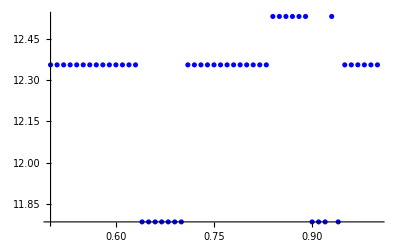

```mathematica
DiscretePlot[
SolveExtraCrowdBT[n,0],
{n, 0.5, 1, 0.01}, 
{PlotStyle-> Blue, Filling->None}]
```

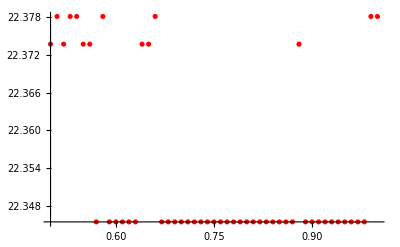

```mathematica
DiscretePlot[
SolveExtraCrowdBT[n,1],
{n, 0.5, 1, 0.01}, 
{PlotStyle-> Red, Filling->None}]
```

In both cases, setting η = 0.9 results in the optimal value.

#### O’Donovan et al.’s Method

```mathematica
Subscript[Subscript[L, ODonovan], Dictators,5,ExtraErrorinU1ToAgreeWithU4][ς1_,ς2_,ς3_, ς4_, ς5_, ς6_, μ1_,μ2_,μ3_, μ4_,μ5_,λ_] := Subscript[L, ODonovan][ς1,ς2, μ1] + Subscript[L, ODonovan][ς3,ς2, μ1] +Subscript[L, ODonovan][ς4,ς3, μ1] + Subscript[L, ODonovan][ς4,ς5, μ1]+ Subscript[L, ODonovan][ς6,ς5, μ1]+Subscript[L, ODonovan][ς2,ς1, μ2] + Subscript[L, ODonovan][ς2,ς3, μ2] +Subscript[L, ODonovan][ς4,ς3, μ2] + Subscript[L, ODonovan][ς5,ς4, μ2]+ Subscript[L, ODonovan][ς6,ς5, μ2]+Subscript[L, ODonovan][ς2,ς1, μ3] + Subscript[L, ODonovan][ς3,ς2, μ3] +Subscript[L, ODonovan][ς3,ς4, μ3] + Subscript[L, ODonovan][ς5,ς4, μ3]+ Subscript[L, ODonovan][ς6,ς5, μ3]+Subscript[L, ODonovan][ς2,ς1, μ4] + Subscript[L, ODonovan][ς3,ς2, μ4] +Subscript[L, ODonovan][ς4,ς3, μ4] + Subscript[L, ODonovan][ς4,ς5, μ4]+ Subscript[L, ODonovan][ς6,ς5, μ4]+Subscript[L, ODonovan][ς2,ς1, μ5] + Subscript[L, ODonovan][ς3,ς2, μ5] +Subscript[L, ODonovan][ς4,ς3, μ5] + Subscript[L, ODonovan][ς5,ς4, μ5]+ Subscript[L, ODonovan][ς5,ς6, μ5]+λ*(Subscript[L, 0][ς1]+ Subscript[L, 0][ς2]+Subscript[L, 0][ς3]+ Subscript[L, 0][ς4]+ Subscript[L, 0][ς5]+ Subscript[L, 0][ς6])
```

```mathematica
{minODonovanDictators5ExtraError0, solODonovanDictators5ExtraError0} = FindMinimum[{Subscript[Subscript[L, ODonovan], Dictators,5,ExtraErrorinU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6,μ1,μ2,μ3, μ4,μ5,0], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, -10≤μ1≤10, -10≤μ2≤10, -10≤μ3≤10, -10≤μ4≤10, -10≤μ5≤10}, {ς1,ς2,ς3, ς4,ς5, ς6, {μ1,1},{μ2,1},{μ3,1}, {μ4,1},{μ5,1}}]
{minODonovanDictators5ExtraError1, solODonovanDictators5ExtraError1} = FindMinimum[{Subscript[Subscript[L, ODonovan], Dictators,5,ExtraErrorinU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6,μ1,μ2,μ3, μ4,μ5,1], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, -10≤μ1≤10, -10≤μ2≤10, -10≤μ3≤10, -10≤μ4≤10, -10≤μ5≤10}, {ς1,ς2,ς3, ς4,ς5, ς6, {μ1,1},{μ2,1},{μ3,1}, {μ4,1},{μ5,1}}]
```

{9.74874,{ς1→-99.9997,ς2→-99.9994,ς3→-99.2895,ς4→-98.5796,ς5→-99.2918,ς6→99.9995,μ1→9.99994,μ2→0.0315763,μ3→0.0315763,μ4→9.99995,μ5→-0.0316033}}

{19.7934,{ς1→0.0687067,ς2→0.0363366,ς3→0.3484,ς4→0.693704,ς5→-0.747675,ς6→-0.40797,μ1→10.,μ2→-1.05835,μ3→-1.14749,μ4→9.99999,μ5→-1.13205}}

The final version of the table entries with rounding in place:

```mathematica
roundingValue = 0.1;
```

```mathematica
TableForm[{Round[N[{ μ1,μ2,μ3, μ4,μ5}]/.solODonovanDictators5ExtraError0, roundingValue],Round[N[{ μ1,μ2,μ3, μ4,μ5}] /.solODonovanDictators5ExtraError1, roundingValue]}]
```

10. | 0. | 0. | 10. | 0.
10. | -1.1 | -1.1 | 10. | -1.1

Note that the outcomes are parameter dependent.  Removing the starting values of μ = 1 can result in a slightly better NLL.

```mathematica
{minODonovanDictators5ExtraError0, solODonovanDictators5ExtraError0} = FindMinimum[{Subscript[Subscript[L, ODonovan], Dictators,5,ExtraErrorinU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6,μ1,μ2,μ3, μ4,μ5,0], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, -10≤μ1≤10, -10≤μ2≤10, -10≤μ3≤10, -10≤μ4≤10, -10≤μ5≤10}, {ς1,ς2,ς3, ς4,ς5, ς6, μ1,μ2,μ3,μ4,μ5}]
{minODonovanDictators5ExtraError1, solODonovanDictators5ExtraError1} = FindMinimum[{Subscript[Subscript[L, ODonovan], Dictators,5,ExtraErrorinU1ToAgreeWithU4][ς1,ς2,ς3, ς4,ς5, ς6,μ1,μ2,μ3, μ4,μ5,1], -100≤ς1≤100,-100≤ς2≤100,-100≤ς3≤100,-100≤ς4≤100,-100≤ς5≤100,-100≤ς6≤100, -10≤μ1≤10, -10≤μ2≤10, -10≤μ3≤10, -10≤μ4≤10, -10≤μ5≤10}, {ς1,ς2,ς3, ς4,ς5, ς6, μ1,μ2,μ3,μ4,μ5}]
```

{9.44909,{ς1→-99.9999,ς2→-99.7218,ς3→-95.5581,ς4→-91.3944,ς5→-95.6478,ς6→99.9999,μ1→1.0394,μ2→0.0226801,μ3→0.0226801,μ4→9.99999,μ5→-0.0222815}}

{19.7934,{ς1→0.0687067,ς2→0.0363366,ς3→0.3484,ς4→0.693704,ς5→-0.747675,ς6→-0.40797,μ1→10.,μ2→-1.05835,μ3→-1.14749,μ4→9.99999,μ5→-1.13205}}